## 2022-07-22 This is a graph growth version. GraphRoots has to be run separately.

Run the cell below to visualise the graph as well as the real and imaginary part of the determinant of D(k). c1 and c2 can be changed using the sliders. When the determinant of D(k) = 0 we get a root k_n and an eigenvalue, λ_n=k_n^2. If the graph contains rationally independent edge-length this is the only way to find approximate roots.

```mathematica
mo=({{∞, ∞, c2, ∞}, {∞, ∞, c1, 1}, {c2, c1, ∞, 1}, {∞, 1, 1, ∞}});
(*GraphRoots[mo];*)
WeightedAdjacencyGraph[mo, EdgeLabels->"EdgeWeight" ]
end=10π;
c3=1;
c4=1;

Manipulate[ 
Plot[ {SDeterminantD[mo,c1,c2]//Re, SDeterminantD[mo,c1,c2]//Im},{k,0π,end},PlotRange->All,Ticks->{end/5*{0,1,2,3,4,5},Automatic}],{c1, 0.001π, 10 π},{c2,0.001Pi, 150π}]
```

-Graphics-

Run the cell below to initialize graph growth.

```mathematica
select[{l1__},hh_,goal_:1]:=(motable=Table[(WeightedAdjacencyMatrix[hh⟦i⟧]//Normal)/.{0->∞},{i,1,Length[hh]}];
target={0,l1,0}//N;
target=Take[target,goal+1];
(*target:={0,0,0,0,0};/goal==4;*)
(*Print[goal,target];*)
eigtable=Table[NGraphRoots[motable⟦i⟧,Length[{l1}]+2],{i,1,Length[motable]}];
dist1=Table[Norm[eigtable⟦i,2⟧-target⟦2⟧],{i,1,Length[motable]}];
dist2=Table[Norm[Take[eigtable⟦i⟧,Length[target]]-target],{i,1,Length[motable]}];

dist4=Table[Norm[eigtable⟦i,2⟧/eigtable⟦i,3⟧],{i,1,Length[motable]}];
distances=If[goal==1,dist1,dist2];
distances:=dist2/;goal==1;
distances:=dist2/;goal==2;
distances:=dist2/;goal==3;
distances:=dist4/;goal==4;
minpos=Position[distances,Min[distances]]⟦1,1⟧;
h=WeightedAdjacencyGraph[motable⟦minpos⟧];
eigs=NGraphRoots[motable⟦minpos⟧,4];
tmp=Append[eigcumulant,eigs];
eigcumulant=tmp;
AppendTo[GraphSequence,h])

tedgeadd[{l1__},n_,goal_:1]:=
Do[hh=Table[EdgeAdd[h,i<->j],{i,1,VertexCount[h]},{j,i,VertexCount[h]}]//Flatten;
uu=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
hh=hh∪uu;
hh=Table[If[SimpleGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n];

tvertexaddinternal[{l1__},n_,goal_:1]:=
Do[edgelist=IncidenceMatrix[h]//IncidenceGraph//EdgeList;
hh=Table[EdgeAdd[EdgeDelete[h,edgelist⟦i⟧]],{i,1,Length[edgelist]}];
hh=Table[If[ConnectedGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgeaddinternal[{l1__},n_,goal_:1]:=Do[hh=Table[EdgeAdd[h,i<->j],{i,1,VertexCount[h]},{j,i,VertexCount[h]}]//Flatten;
hh=Table[If[SimpleGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgeaddtree[{l1__},n_,goal_:1]:=
Do[hh=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
hh=Table[If[SimpleGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgecontract[{l1__},n_,goal_:1]:=
Do[
hh=Table[EdgeContract[h,EdgeList[h]⟦i⟧],{i,1,Length[EdgeList[h]]}];
hh=Table[If[SimpleGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgecontractbackup[{l1__},n_,goal_:1]:=
Do[edgelist=IncidenceMatrix[h]//IncidenceGraph//EdgeList;
hh=Table[EdgeContract[h,edgelist⟦i⟧],{i,1,Length[edgelist]}];
hh=Table[If[SimpleGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgedelete[{l1__},n_,goal_:1]:=
Do[
hh=Table[EdgeDelete[h,EdgeList[h]⟦i⟧],{i,1,Length[EdgeList[h]]}];
hh=Table[If[ConnectedGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tedgedeletebackup[{l1__},n_,goal_:1]:=
Do[edgelist=IncidenceMatrix[h]//IncidenceGraph//EdgeList;
hh=Table[EdgeDelete[h,edgelist⟦i⟧],{i,1,Length[edgelist]}];
hh=Table[If[ConnectedGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh,goal],n]

tvertexdelete[l1__]:=(
hh=Table[VertexDelete[h,VertexList[h]⟦i⟧],{i,1,Length[VertexList[h]]}];
hh=Table[If[ConnectedGraphQ[hh⟦i⟧],hh⟦i⟧,Nothing],{i,1,Length[hh]}];
select[{l1},hh])

Firsteigenvalues:=Table[eigcumulant⟦i,1⟧,{i,1,Length[eigcumulant]}];
Secondeigenvalues:=Table[eigcumulant⟦i,2⟧,{i,1,Length[eigcumulant]}];
Thirdeigenvalues:=Table[eigcumulant⟦i,3⟧,{i,1,Length[eigcumulant]}];
Fourtheigenvalues:=Table[eigcumulant⟦i,4⟧,{i,1,Length[eigcumulant]}];
eigenvalueplot:=ListPlot[{Secondeigenvalues,Thirdeigenvalues,Fourtheigenvalues},Frame->True,PlotRange->All,PlotMarkers->Automatic,Joined->True];
p2:=ListLinePlot[{{1,target⟦2⟧},{Length[eigcumulant],target⟦2⟧}}]/;Length[target]≥2;
p3:=ListLinePlot[{{1,target⟦3⟧},{Length[eigcumulant],target⟦3⟧}}]/;Length[target]≥3;
p4:=ListLinePlot[{{1,target⟦4⟧},{Length[eigcumulant],target⟦4⟧}}]/;Length[target]==4;

plot:=Show[eigenvalueplot,p2,PlotRange->All]/;Length[target]==2;
plot:=Show[eigenvalueplot,p2,p3,PlotRange->All]/;Length[target]==3;
plot:=Show[eigenvalueplot,p2,p3,p4,PlotRange->All]/;Length[target]==4;
plot:=Show[eigenvalueplot,PlotRange->All]/;Length[target]==5;
```

```mathematica
Dumbell=Button[MakeDumbell,(h1=EdgeList[h];
h2=EdgeList[h] /.( xx_Integer->xx+Max[VertexList[h]]);
h3={VertexList[h1]⟦1⟧<->VertexList[h2]⟦1⟧};
h=Graph[h1∪h2∪h3])];

DecoratedStar=Button[MakeDecoratedStar,(h1=EdgeList[h];
h2=EdgeList[h] /.( xx_Integer->xx+Max[VertexList[h]]);
h3=EdgeList[h] /.( xx_Integer->xx+2Max[VertexList[h]]);
h4={VertexList[h1]⟦1⟧<->3Length[EdgeList[h]]+1,VertexList[h2]⟦1⟧<->3Length[EdgeList[h]]+1,VertexList[h3]⟦1⟧<->3Length[EdgeList[h]]+1};
h=Graph[h1∪h2∪h3∪h4])];

DecoratedStarSmall=Button[MakeDumbellStarGraph,(h1=EdgeList[h];
h2=EdgeList[h] /.( xx_Integer->xx+Max[VertexList[h]]);
h3=EdgeList[h] /.( xx_Integer->xx+2Max[VertexList[h]]);
h4={VertexList[h1]⟦1⟧<->3Length[EdgeList[h]]+1,VertexList[h2]⟦1⟧<->3Length[EdgeList[h]]+1,VertexList[h3]⟦1⟧<->3Length[EdgeList[h]]+1};
h=Graph[h1∪h2∪h3∪h4])];

ResetButton=Button[Reset,(GraphSequence={};
eigcumulant={};h=.;eigs={1,2,3,4,5};roots=.)];

MyEigenvalues=Button["Get numerical roots and initialise graph growth with the selected graph",(If[Head[h]===Graph,mo=(WeightedAdjacencyMatrix[h]//Normal)/.{0->∞},eigs=.];
eigs=NGraphRoots[mo,7];
GraphSequence={h};
roots=.;
eigcumulant={eigs}),Method->"Queued"];

ExactEigenvalues=Button["Get both numerical and exact roots and initialise graph growth with the selected graph",(If[Head[h]===Graph,mo=(WeightedAdjacencyMatrix[h]//Normal)/.{0->∞},eigs=.];
eigs=NGraphRoots[mo,7];
roots=GraphRoots[mo];
GraphSequence={h};
eigcumulant={eigs}),Method->"Queued"];
```

In the top row you can set two numbers that will change the graphs. Many of the graphs depend on two parameters. Clicking on one of the graphs selects this graph and it will become highlighted. 
    Clicking ' MakeDumbell' or' MakeDecoratedStar' will construct a new graph. Test and get a feel for what happens.
    Clicking ' Get both numerical and exact eigenvalues' will give you the eigenvalues of the selected graph. This may take time if the graph is large. 
    Clicking ' Reset' will clear the graph as well as the lists containing the eigenvalues.

```mathematica
{SetterBar[Dynamic[x1],Range[10]],SetterBar[Dynamic[x2],Range[10]],
Dynamic[SetterBar[Dynamic[h],{PathGraph[Range[x1]],StarGraph[x1],CycleGraph[x1],CompleteGraph[x1],GridGraph[{x1,x2}],WheelGraph[x1],KaryTree[x1,x2]}]],Dumbell,DecoratedStar,MyEigenvalues,ExactEigenvalues, ResetButton}

Dynamic[h//Small]
Dynamic[GraphSequence//Small]
Dynamic[eigs]
Dynamic[roots]
```

{ |  |  |  |  |  |  |  |  | , |  |  |  |  |  |  |  |  | ,,MakeDumbell,MakeDecoratedStar,Get numerical roots and initialise graph growth with the selected graph,Get both numerical and exact roots and initialise graph growth with the selected graph,Reset}

```mathematica
roots;
```

```mathematica
Manipulate[{{Button["Add an edge", tedgeadd[{e1, e2, e3}, n, goal], Method -> "Queued"], Button["Add an edge which ends in a new vertex", tedgeaddtree[{e1, e2, e3}, n, goal], Method -> "Queued"], 
        Button["Add an edge connecting two existing vertices", tedgeaddinternal[{e1, e2, e3}, n, goal], Method -> "Queued"], Button["Delete an edge between two existing vertices", tedgecontract[{e1, e2, e3}, n, goal], Method -> "Queued"], 
       Button["Delete any edge", tedgedelete[{e1,e2, e3}, n, goal], Method -> "Queued"]}, {"e_1 = "Dynamic[e1/π+0.]π  , "e_2 = "Dynamic[e2/π +0.]π,"e_3 = "Dynamic[e3/π +0.]π, 
    "k_1 = "Dynamic[eigs⟦2⟧/π]π, "k_2 = "Dynamic[eigs⟦3⟧/π]π, "k_3 = "Dynamic[eigs⟦4⟧/π]π}}, {e1, π, 10π, π/10, Appearance -> "Labeled"}, 
  {e2, π, 10π, π/10, Appearance -> "Labeled"},{e3, π, 10π, π/10, Appearance -> "Labeled"}, {{n, 1, "Iterations"}, {1, 2, 3, 4, 5, 10, 20}}, 
  {{goal, 1, "1: Min ||k_1 - e_1||
2: Min ||(k_1, k_2)-(e_1, e_2)||
3: Min ||(k_1, k_(2,) k_3)-(e_1, e_2, e_3)||
4: Max k_2/k_1"}, {1, 2, 3,4}}]
```

Part::partw: Part 1 of {} does not exist.

WeightedAdjacencyGraph::matsq: Argument {}⟦{}⟦1,1⟧⟧ at position 1 is not a non-empty square matrix.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[WeightedAdjacencyGraph[{}⟦{}⟦1,1⟧⟧]].

EdgeDelete::graph: A graph object is expected at position 1 in EdgeDelete[WeightedAdjacencyGraph[{}⟦{}⟦1,1⟧⟧],WeightedAdjacencyGraph[{}⟦{}⟦1,1⟧⟧]].

Part::partw: Part 1 of {} does not exist.

WeightedAdjacencyGraph::matsq: Argument {}⟦{}⟦1,1⟧⟧ at position 1 is not a non-empty square matrix.

```mathematica
Dynamic[GraphSequence//Small]
Dynamic[plot]
```

```mathematica
e1=Pi;e2=6Pi;e3=20 Pi;n=1;
```

```mathematica
While[ n<9,
tedgeadd[{e1,e2},1,2];
tedgeaddtree[{e1,e2},1,2];
tedgecontract[{e1,e2},1,2];
n=n+1];
```

```mathematica
e1=2Pi;e2=8Pi;
While[ (eigs⟦3⟧<7 Pi),
tedgeadd[{e1,e2},1,2];
tedgeaddtree[{e1,e2},1,2];
tedgecontract[{e1,e2},1,2]]
```

$Aborted

```mathematica
While[eigs⟦2⟧<5Pi,tedgeadd[{5 Pi},1,1]];
While[ (eigs⟦3⟧<13 Pi),tedgeadd[{5 Pi,15 Pi},1,2];tedgeaddtree[{5 Pi,15 Pi},1,2]]
```

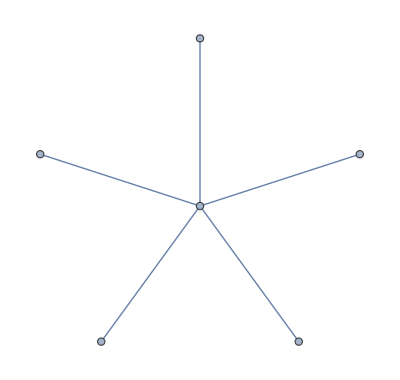
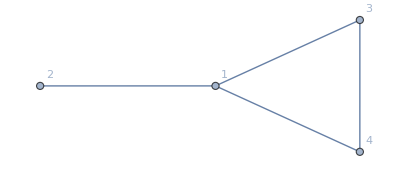
```mathematica
myrules=GraphRoots[-Graphics-]//Simplify//Expand;
myruleslasso=GraphRoots[-Graphics-]//Chop//Simplify//Expand//Chop//ToRadicals//Simplify
```

{{k→ConditionalExpression[8 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(8 π)/3+8 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(8 π)/3+8 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[8 π C[1]-4 ⅈ Log[1/12 (-3-√33-ⅈ √(102-6 √33))], C[1]∈ℤ]},{k→ConditionalExpression[8 π C[1]-4 ⅈ Log[1/12 (-3-√33+ⅈ √(102-6 √33))], C[1]∈ℤ]},{k→ConditionalExpression[8 π C[1]-4 ⅈ Log[1/12 (-3+√33-ⅈ √(6 (17+√33)))], C[1]∈ℤ]},{k→ConditionalExpression[8 π C[1]-4 ⅈ Log[1/12 (-3+√33+ⅈ √(6 (17+√33)))], C[1]∈ℤ]}}